# Derivative Formulas

## First Derivative Formulas

### Forward (Backward) Difference

Let’s first take a look at the forward difference formula in action by doing example 1 from the book in Mathematica.

First we define

```mathematica
DiffFormula[f_,x_,h_]:=(f[x+h]-f[x])/h
ErrorBound[f_,M_,h_]:=Abs[h*M]/2
```

The function we are looking at here is f(x)=ln(x). Not that ln(x)=Log[x] in Mathematica... after all, why would you ever use any other log!

```mathematica
f[x_]:=Log[x]
h={0.1,0.05,0.01};
```

It’s easy enough to Table over the difference formula to get the approximations.

```mathematica
Approx=Table[DiffFormula[f,1.8,h[[i]]],{i,1,3}];
Approx//TableForm
```

0.540672
0.547979
0.554018

Since we know f we can ask Mathematica to find the bound.

```mathematica
M=Maximize[Abs[f''[x]],1.8≤x≤1.9,x][[1]]
```

0.308642

Finally, we compute the errors for each approximation.

```mathematica
ErrorsBounds=Table[ErrorBound[f,M,h[[i]]],{i,1,3}];
ErrorsBounds//TableForm
```

Part::partd: Part specification 1/100000 ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification 1/100000 ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

0.154321 Abs[1/100000⟦1⟧]
0.154321 Abs[1/100000⟦2⟧]
0.154321 Abs[1/100000⟦3⟧]

Let’s take a look at the actual error.

```mathematica
ActualError[f_,approx_,x_]:=Abs[f'[x]-approx]
```

```mathematica
Table[ActualError[f,Approx[[i]],1.8],{i,1,3}]//TableForm
```

0.0148833
0.00757607
0.00153752

So, we see here that these error bounds are quite good!

One might think that you can get a better answer by taking a smaller h... this works for a while, but eventually round-off error takes over.

```mathematica
Manipulate[
h := 10^(-n);
DerivData := Table[{i/10.0,DiffFormula[f,i/10.0,h]},{i,0,100}];
Show[Plot[f'[x],{x,0,10}],ListLinePlot[DerivData,PlotRange->All],
ListPlot[DerivData,PlotStyle->{PointSize[Large]}]],{n,5,18,Appearance->"Labeled"}]
```

Using the same trick as we saw a few weeks ago we can look at the number of correct digits.

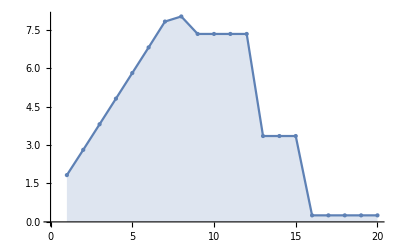

```mathematica
NewData :=Table[{n,Abs[Log[10,Abs[DiffFormula[f,1.8,10.0^(-n)] - f'[1.8]]]]},{n,1,20}]
Show[ListLinePlot[NewData,Filling->Axis,PlotRange->Full,AxesOrigin->{0,0}],
ListPlot[NewData,PlotStyle->{PointSize[Large]}]]
```

We can see here that we get the best result for h=10^(-8), but this is difficult to predict in general.

### Three Point Midpoint Formula

Let’s take a look at a three point formula.

```mathematica
MidpointFormula[f_,x_,h_]:=1/(2h)*(f[x+h]-f[x-h])
```

```mathematica
Manipulate[
h := 10^(-n);
DerivData := Table[{i/10.0,MidpointFormula[f,i/10.0,h]},{i,0,100}];
Show[Plot[f'[x],{x,0,10}],ListLinePlot[DerivData,PlotRange->All],
ListPlot[DerivData,PlotStyle->{PointSize[Large]}]],{n,5,18,Appearance->"Labeled"}]
```

Again we see that roundoff error takes over around h=10^(-14), but we can see a difference if we look at the correct digits!

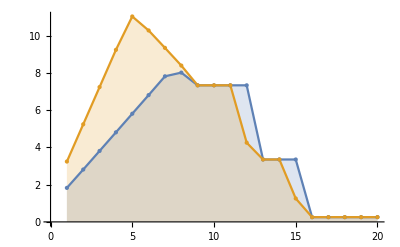

```mathematica
MidpointData :=Table[{n,Abs[Log[10,Abs[MidpointFormula[f,1.8,10.0^(-n)] - f'[1.8]]]]},{n,1,20}]
Show[ListLinePlot[{NewData,MidpointData},Filling->Axis,PlotRange->Full,AxesOrigin->{0,0}],
ListPlot[{NewData,MidpointData},PlotStyle->{PointSize[Large]}]]
```

We get better approximation earlier!

### Five Point Midpoint Formula

Let’s take a look at a five point formula.

```mathematica
FivePointFormula[f_,x_,h_]:=1/(12h)*(f[x-2h]-8f[x-h]+8f[x+h]-f[x+2h])
```

```mathematica
Manipulate[
h := 10^(-n);
DerivData := Table[{i/10.0,FivePointFormula[f,i/10.0,h]},{i,0,100}];
Show[Plot[f'[x],{x,0,10}],ListLinePlot[DerivData,PlotRange->All],
ListPlot[DerivData,PlotStyle->{PointSize[Large]}]],{n,5,18,Appearance->"Labeled"}]
```

As we should expect, roundoff error takes over at about the same value of h. What about the correct digits?

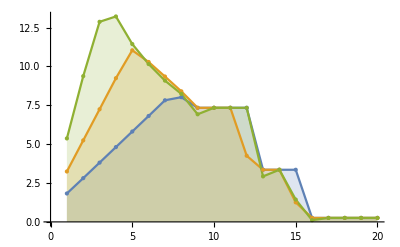

```mathematica
FivePointData :=Table[{n,Abs[Log[10,Abs[FivePointFormula[f,1.8,10.0^(-n)] - f'[1.8]]]]},{n,1,20}]
Show[ListLinePlot[{NewData,MidpointData,FivePointData},Filling->Axis,PlotRange->Full,AxesOrigin->{0,0}],
ListPlot[{NewData,MidpointData,FivePointData},PlotStyle->{PointSize[Large]}]]
```

Now we have more than 12 correct digits with h=10^(-4)! The moral of this story is that using clever derivative formulas is better than just taking a smaller h.

Remember that in practice we DON’T KNOW the actual value of the derivative, so such analysis of the number of correct digits is not possible!

## Second Derivative Formula

### Midpoint Formula

Let’s look at the second derivative midpoint formula that came from Taylor’s Theorem.

```mathematica
SDMidpointFormula[f,x_,h_]:=(1/h^2)(f[x-h]-2f[x]+f[x+h])
```

```mathematica
Manipulate[
h := 10^(-n);
SecDerivData := Table[{i/10.0,SDMidpointFormula[f,i/10.0,h]},{i,0,100}];
Show[Plot[f''[x],{x,0,10}],ListLinePlot[SecDerivData,PlotRange->All],
ListPlot[SecDerivData,PlotStyle->{PointSize[Large]}]],{n,5,18,Appearance->"Labeled"}]
```

Notice that this formula is more sensitive to round off error! Let’s look at the correct digits. We will look at x=4

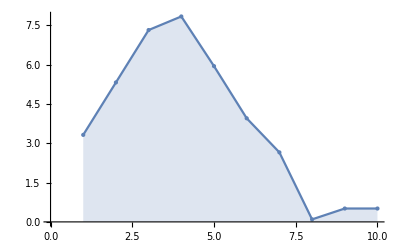

```mathematica
NewData :=Table[{n,Abs[Log[10,Abs[SDMidpointFormula[f,1.8,10.0^(-n)] - f''[1.8]]]]},{n,1,10}]
Show[ListLinePlot[NewData,Filling->Axis,PlotRange->Full,AxesOrigin->{0,0}],
ListPlot[NewData,PlotStyle->{PointSize[Large]}]]
```

This isn’t great... the best we can do is 8 correct digits. We could take more terms in the Taylor Expansion to get better formulas as we did before (in fact, this sounds like a good homework problem!). But, let’s do something else!

There is a general method to improving an approximation that doesn’t involve adding new points. This method is called Richardson’s Extrapolation.